```mathematica
data=Import["/home/eduardo/Documentos/Universidad/Maestría/Cálculos/FFTW/recoil_force_dipolar_aprox_results.txt","Table"];
Dimensions[data]
```

{131072,3}

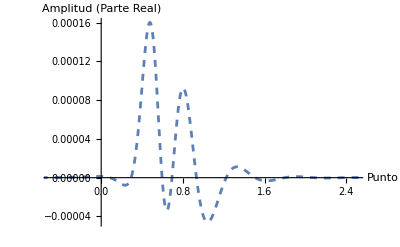

```mathematica
ComponenteTransversal=ListPlot[Transpose[{data[[All,1]],data[[All,2]]}],PlotStyle->Dashed,AxesLabel->{"Punto","Amplitud (Parte Real)"},Joined->True,PlotRange->{{-0.5,2.5},All}]
```

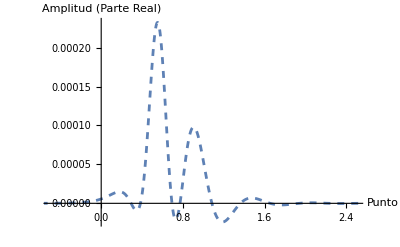

```mathematica
ComponenteLongitudinal=ListPlot[Transpose[{data[[All,1]],data[[All,3]]}],PlotStyle->Dashed,AxesLabel->{"Punto","Amplitud (Parte Real)"},Joined->True,PlotRange->{{-0.5,2.5},All}]
```

```mathematica
Plot3D
```